```mathematica
G[t_] := HeavisideTheta[t+1/2] -  HeavisideTheta[t-1/2]
```

```mathematica
T[t_]:=(1-2*Abs[t])*G[t]
```

```mathematica
F[t_]:=-T[1/2 t+1/2]-T[t]+T[1/2 t-1]
```

```mathematica
K[t_]:=Sum[DiscreteDelta[t-k]+DiscreteDelta[t-2k],{k,-∞,∞}]
```

```mathematica
FourierSequenceTransform[Sum[DiscreteDelta[t-k]+DiscreteDelta[t-2k],{k,-∞,∞}],t,ω,FourierParameters->{1, 1}]
```

ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))-ⅇ^(2 ⅈ ω)/(-1+ⅇ^(ⅈ ω))+2 π DiracDelta[ω]

```mathematica
Sum[K[n]Exp[-ⅈ n ω 1/L],{n,0,L-1}]//.L->2
```

(2 ⅇ^(-(ⅈ ω)/2) (-1+ⅇ^(ⅈ ω)))/(-1+ⅇ^((ⅈ ω)/2))

```mathematica
FourierTransform[Sum[DiracDelta[t-k]+DiracDelta[t-2k],{k,-∞,∞}],t,ω,FourierParameters->{1, -1}]
```

∑_(k=-∞)^∞ (Cos[k ω]+Cos[2 k ω]-ⅈ (Sin[k ω]+Sin[2 k ω]))

```mathematica
TrigToExp[Cos[k ω]+ⅈ Sin[k ω]]
```

ⅇ^(ⅈ k ω)

```mathematica
∑_(k=-∞)^∞ ⅇ^(-2 ⅈ k ω) (UnitStep[-1-2 k]+ⅇ^(ⅈ k ω) UnitStep[-1-k]+ⅇ^(ⅈ k ω) UnitStep[k]+UnitStep[2 k])
```

0

```mathematica
∑_(k=-∞)^-1 ⅇ^(-2 ⅈ k ω)
∑_(k=-∞)^-1 ⅇ^(- ⅈ k ω)
∑_(k=0)^∞ ⅇ^(-ⅈ k ω)
∑_(k=0)^∞ ⅇ^(-2 ⅈ k ω)
```

-ⅇ^(2 ⅈ ω)/(-1+ⅇ^(2 ⅈ ω))

-ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))

ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))

ⅇ^(2 ⅈ ω)/(-1+ⅇ^(2 ⅈ ω))

```mathematica
FullSimplify[(2+ⅇ^(ⅈ ω))/((-1+ⅇ^(ⅈ ω)) (1+ⅇ^(ⅈ ω)))]
```

(2+ⅇ^(ⅈ ω))/(-1+ⅇ^(2 ⅈ ω))

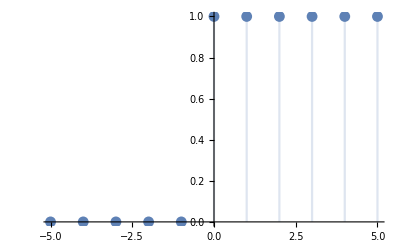

```mathematica
DiscretePlot[UnitStep[2k],{k,-5,5}]
```